# Solución ciclo límite

El sistema


tiene un ciclo límite.

Usa el teorema de Poincaré-Bendixson para encontrar una región anular dentro de la cual se encuentra el ciclo límite.

En coordenadas polares,  y . Tenemos que el radio y el ángulo están dados por 


Derivando la primera ecuación con la regla de cadena y dividiendo de ambos lados entre dos, obtenemos

Sustituimos las ecuaciones diferenciales y obtenemos

Seguimos simplificando usando las identidades de las coordenadas polares



Es la primera ecuación diferencial en coordenadas polares. Ahora derivamos la segunda ecuación y proseguimos de manera similar.








El sistema en coordenadas polares es


La segunda ecuación está desacoplada, tiene solución , lo que indica que las soluciones giran a velocidad angular constante en dirección contraria de las manecillas del reloj, independientemente de la posición radial. Recordemos que, si tenemos un círculo centrado en el origen, las soluciones salen de ese círculo si el radio crece, es decir si , y entra al círculo si el radio decrece, . Por lo tanto, basta encontrar un círculo donde la derivada radial sea negativa, y un círculo donde la derivada radial sea positiva. Entonces, en uno de los círculos se debe cumplir que


Recordemos que el radio es la distancia de las soluciones al origen, por lo que no puede ser negativo. Por lo tanto, podemos dividir entre  (puesto que  corresponde al origen, el cual no pertence a ninguno de los círculos concéntricos) y obtenemos

Recordamos que , por lo que, a lo más, . Esto nos permite obtener la siguiente desigualdad

Vemos que esta expresión es exactamente cero en las raíces del polinomio





Como ya se mencionó, el radio sólo puede ser positivo, por lo tanto, el radio máximo donde la derivada radial es negativa es . El límite exterior de la región atrapante es un círculo de radio tres.
Ahora procedemos de manera similar con el segundo radio, donde necesitamos que la derivada sea positiva, por lo que


De igual manera, el coseno en la expresión vale como mínimo , por lo que podemos acotar de la siguiente manera

Esta cota inferior es igual a cero en las raíces del polinomio, dadas por




El radio positivo es el único que tiene sentido, por lo que el radio interior debe ser al menos de uno. Por lo tanto, la región anular atrapante donde está contenido el ciclo límite es el anillo con radio .

Comprueba el resultado del inciso anterior graficando el retrato fase y la región que encontraste. Basándote en la información visual del retrato fase, ¿el ciclo límite es estable o inestable?

```mathematica
sol1=NDSolve[{x'[t]==x[t]*(x[t]^2+y[t]^2-2*x[t]-3)-y[t],y'[t]==y[t]*(x[t]^2+y[t]^2-2*x[t]-3)+x[t],x[1000]==2,y[1000]==0},{x,y},{t,0,1000}];
```

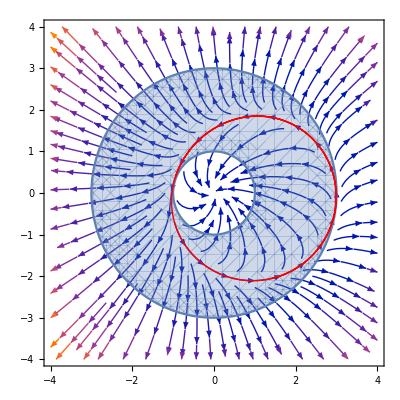

```mathematica
Show[{StreamPlot[{x*(x^2+y^2-2*x-3)-y,y*(x^2+y^2-2*x-3)+x},{x,-4,4},{y,-4,4}],RegionPlot[(x^2+y^2<9)&&(x^2+y^2>1),{x,-4,4},{y,-4,4}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol1],{t,0,10},PlotStyle->{Red,Thick}]}]
```

La región anular que determinamos anteriormente está en azul, y el ciclo límite está en rojo. Claramente, el ciclo se encuentra dentro de la región anular. El ciclo límite es inestable, puesto que las soluciones cercanas son repelidas hacia infinito, o hacia el punto de equilibrio en el origen. En este caso, la región atrapa las soluciones en el límite , contrariamente a los casos que vimos en clase, donde las soluciones se atrapaban en el límite .